## Lista 1 - Exercício 3

### 1 Definindo o Problema

#### 1.1 Função a ser Derivada

```mathematica
Clear[x, y]
f = E^x + E^Sin[x y^3]
```

ⅇ^x+ⅇ^Sin[x y^3]

### 2 Derivadas Parciais no domínio (x, y)

#### 2.1 df/dx

```mathematica
dfdx = D[f,x]
```

ⅇ^x+ⅇ^Sin[x y^3] y^3 Cos[x y^3]

#### 2.1 df/dy

```mathematica
dfdy = D[f,y]
```

3 ⅇ^Sin[x y^3] x y^2 Cos[x y^3]

### 3 Relação do Domínio (x, y) e (ξ, η) e suas Derivadas Parciais

#### 3.1 x

```mathematica
x = Cos[ξ^2] + Sin[η + 1] + 5ξ
```

5 ξ+Cos[ξ^2]+Sin[1+η]

#### 3.2 y

```mathematica
y = Sin[ξ^3] - Cos[η^2] + 7η
```

7 η-Cos[η^2]+Sin[ξ^3]

#### 3.3 dx/dξ

```mathematica
dxdξ = D[x, ξ]
```

5-2 ξ Sin[ξ^2]

#### 3.4 dx/dη

```mathematica
dxdη = D[x, η]
```

Cos[1+η]

#### 3.5 dy/dξ

```mathematica
dydξ = D[y, ξ]
```

3 ξ^2 Cos[ξ^3]

#### 3.6 dx/dη

```mathematica
dydη = D[y, η]
```

7+2 η Sin[η^2]

### 4 Gradiente de f no domínio (ξ, η)

#### 4.1 df/dξ

```mathematica
dfdξ = dfdx dxdξ + dfdy dydξ
```

9 ⅇ^Sin[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] ξ^2 Cos[ξ^3] Cos[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] (5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^2+(5-2 ξ Sin[ξ^2]) (ⅇ^(5 ξ+Cos[ξ^2]+Sin[1+η])+ⅇ^Sin[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] Cos[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] (7 η-Cos[η^2]+Sin[ξ^3])^3)

#### 4.2 df/dη

```mathematica
dfdη = dfdx dxdη + dfdy dydη
```

3 ⅇ^Sin[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] Cos[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] (7+2 η Sin[η^2]) (5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^2+Cos[1+η] (ⅇ^(5 ξ+Cos[ξ^2]+Sin[1+η])+ⅇ^Sin[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] Cos[(5 ξ+Cos[ξ^2]+Sin[1+η]) (7 η-Cos[η^2]+Sin[ξ^3])^3] (7 η-Cos[η^2]+Sin[ξ^3])^3)

#### 4.3 Comparação de Resultados para∇f

```mathematica
gradF = Grad[f, {ξ, η}];
gradChainF = {dfdξ, dfdη};

gradChainF - gradF//Simplify
```

{0,0}

### 5 Resultados

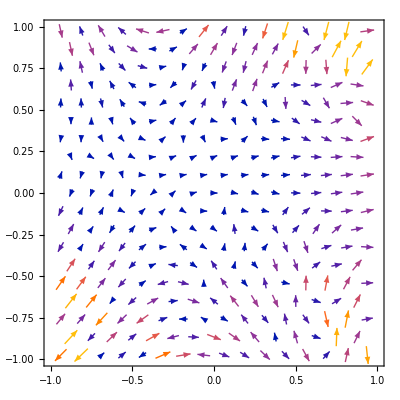

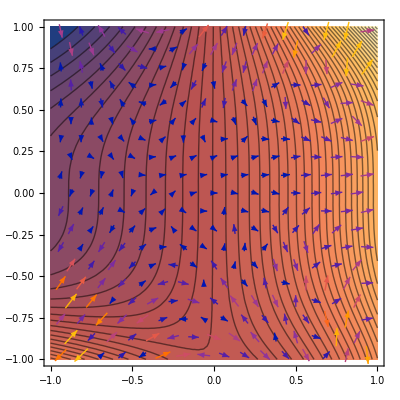

```mathematica
a = VectorPlot[gradF, {ξ, -1, 1}, {η, -1, 1}, VectorScaling->Automatic]
b=ContourPlot[f,{x,-1,1},{y,-1,1},Contours->50];

Show[b, a]
```